Name : Agam Gupta
Regula-Falsi Method

1. Perform 15 - iteration of the Regula - falsi method to Obtain the smallest postive root of the f x = Cos[x] - x in interval[0, 1] and take intial approx x = 0 and x1 = 1

1.th iteration value is :0.685073

Estimated error in 1th iteration is: 0.314927

2.th iteration value is :0.736299

Estimated error in 2th iteration is: 0.263701

3.th iteration value is :0.738945

Estimated error in 3th iteration is: 0.261055

4.th iteration value is :0.739078

Estimated error in 4th iteration is: 0.260922

5.th iteration value is :0.739085

Estimated error in 5th iteration is: 0.260915

6.th iteration value is :0.739085

Estimated error in 6th iteration is: 0.260915

7.th iteration value is :0.739085

Estimated error in 7th iteration is: 0.260915

8.th iteration value is :0.739085

Estimated error in 8th iteration is: 0.260915

9.th iteration value is :0.739085

Estimated error in 9th iteration is: 0.260915

10.th iteration value is :0.739085

Estimated error in 10th iteration is: 0.260915

11.th iteration value is :0.739085

Estimated error in 11th iteration is: 0.260915

12.th iteration value is :0.739085

Estimated error in 12th iteration is: 0.260915

13.th iteration value is :0.739085

Estimated error in 13th iteration is: 0.260915

Return[0.739085]

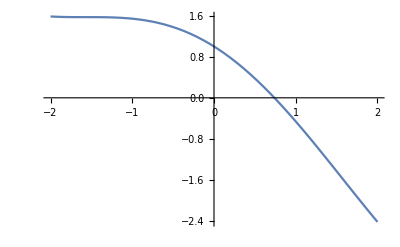

```mathematica
x = 0;
x1 = 1;
e = 0.00005;
Nmax = 15;
f[x_]:= Cos[x]-x;
If[f[x]*f[x1]>0,
Print["These vales do not satisfy the IVP so change the initial values"],
For[i=1,i≤Nmax,i++,a=N[(x *f[x1]- x1*f[x])/(f[x1]-f[x])];
If[f[a]f[x1]<0,x=a,x1=a];
If[Abs[x1-x]<e,Return[a]];
Print[i. "th iteration value is :",N[a]];
Print["Estimated error in ",i,"th iteration is: ",N[x1-x]]]]
Plot[f[x],{x,-2,2}]
```

2. Perform 45-iteration of Regula-Falsi method to Obtain the smallest positive root of f(x) = x^3+2^x-3x-1 in interval [0,1] and approx value x = 0, x1 = 1.

1.th iteration value is :1.1

Estimated error in 1th iteration is: 0.9

2.th iteration value is :1.15174

Estimated error in 2th iteration is: 0.848256

3.th iteration value is :1.17684

Estimated error in 3th iteration is: 0.823159

4.th iteration value is :1.18863

Estimated error in 4th iteration is: 0.811372

5.th iteration value is :1.19408

Estimated error in 5th iteration is: 0.805921

6.th iteration value is :1.19658

Estimated error in 6th iteration is: 0.803418

7.th iteration value is :1.19773

Estimated error in 7th iteration is: 0.802272

8.th iteration value is :1.19825

Estimated error in 8th iteration is: 0.801749

9.th iteration value is :1.19849

Estimated error in 9th iteration is: 0.80151

10.th iteration value is :1.1986

Estimated error in 10th iteration is: 0.8014

11.th iteration value is :1.19865

Estimated error in 11th iteration is: 0.801351

12.th iteration value is :1.19867

Estimated error in 12th iteration is: 0.801328

13.th iteration value is :1.19868

Estimated error in 13th iteration is: 0.801317

14.th iteration value is :1.19869

Estimated error in 14th iteration is: 0.801313

15.th iteration value is :1.19869

Estimated error in 15th iteration is: 0.801311

16.th iteration value is :1.19869

Estimated error in 16th iteration is: 0.80131

17.th iteration value is :1.19869

Estimated error in 17th iteration is: 0.801309

18.th iteration value is :1.19869

Estimated error in 18th iteration is: 0.801309

19.th iteration value is :1.19869

Estimated error in 19th iteration is: 0.801309

20.th iteration value is :1.19869

Estimated error in 20th iteration is: 0.801309

21.th iteration value is :1.19869

Estimated error in 21th iteration is: 0.801309

22.th iteration value is :1.19869

Estimated error in 22th iteration is: 0.801309

23.th iteration value is :1.19869

Estimated error in 23th iteration is: 0.801309

24.th iteration value is :1.19869

Estimated error in 24th iteration is: 0.801309

25.th iteration value is :1.19869

Estimated error in 25th iteration is: 0.801309

26.th iteration value is :1.19869

Estimated error in 26th iteration is: 0.801309

27.th iteration value is :1.19869

Estimated error in 27th iteration is: 0.801309

28.th iteration value is :1.19869

Estimated error in 28th iteration is: 0.801309

29.th iteration value is :1.19869

Estimated error in 29th iteration is: 0.801309

30.th iteration value is :1.19869

Estimated error in 30th iteration is: 0.801309

31.th iteration value is :1.19869

Estimated error in 31th iteration is: 0.801309

32.th iteration value is :1.19869

Estimated error in 32th iteration is: 0.801309

33.th iteration value is :1.19869

Estimated error in 33th iteration is: 0.801309

34.th iteration value is :1.19869

Estimated error in 34th iteration is: 0.801309

35.th iteration value is :1.19869

Estimated error in 35th iteration is: 0.801309

36.th iteration value is :1.19869

Estimated error in 36th iteration is: 0.801309

37.th iteration value is :1.19869

Estimated error in 37th iteration is: 0.801309

38.th iteration value is :1.19869

Estimated error in 38th iteration is: 0.801309

39.th iteration value is :1.19869

Estimated error in 39th iteration is: 0.801309

40.th iteration value is :1.19869

Estimated error in 40th iteration is: 0.801309

41.th iteration value is :1.19869

Estimated error in 41th iteration is: 0.801309

42.th iteration value is :1.19869

Estimated error in 42th iteration is: 0.801309

43.th iteration value is :1.19869

Estimated error in 43th iteration is: 0.801309

44.th iteration value is :1.19869

Estimated error in 44th iteration is: 0.801309

Return[1.19869]

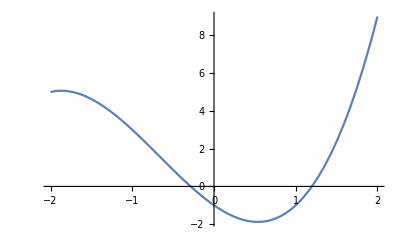

```mathematica
x = 1;
x1 = 2;
e = 0.0005;
Nmax = 45;
f[x_]:= x^3+2x^2-3x-1;
If[f[x]*f[x1]>0,
Print["These vales do not satisfy the IVP so change the initial values"],
For[i=1,i≤Nmax,i++,a=N[(x *f[x1]- x1*f[x])/(f[x1]-f[x])];
If[f[a]f[x1]<0,x=a,x1=a];
If[Abs[x1-x]<e,Return[a]];
Print[i. "th iteration value is :",N[a]];
Print["Estimated error in ",i,"th iteration is: ",N[x1-x]]]]
Plot[f[x],{x,-2,2}]
```

3. Perform 15-iteration of Regula-Falsi method to Obtain the smallest positive root of f(x) = Log[1+x]-Cos[x] in interval [0,1] and approx value x = 0, x1 = 1.

1.th iteration value is :0.867419

Estimated error in 1th iteration is: 0.132581

2.th iteration value is :0.88426

Estimated error in 2th iteration is: 0.11574

3.th iteration value is :0.884507

Estimated error in 3th iteration is: 0.115493

4.th iteration value is :0.884511

Estimated error in 4th iteration is: 0.115489

5.th iteration value is :0.884511

Estimated error in 5th iteration is: 0.115489

6.th iteration value is :0.884511

Estimated error in 6th iteration is: 0.115489

7.th iteration value is :0.884511

Estimated error in 7th iteration is: 0.115489

8.th iteration value is :0.884511

Estimated error in 8th iteration is: 0.115489

Return[0.884511]

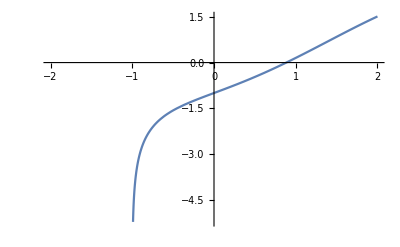

```mathematica
x = 0;
x1 = 1;
e = 0.00005;
Nmax = 15;
f[x_]:= Log[1+x]-Cos[x];
If[f[x]*f[x1]>0,
Print["These vales do not satisfy the IVP so change the initial values"],
For[i=1,i≤Nmax,i++,a=N[(x *f[x1]- x1*f[x])/(f[x1]-f[x])];
If[f[a]f[x1]<0,x=a,x1=a];
If[Abs[x1-x]<e,Return[a]];
Print[i. "th iteration value is :",N[a]];
Print["Estimated error in ",i,"th iteration is: ",N[x1-x]]]]
Plot[f[x],{x,-2,2}]
```

4. Perform 15-iteration of Regula-Falsi method to Obtain the smallest positive root of f(x) = Exp[-x]-x  in interval [0,1] and approx value x = 0, x1 = 1.

1.th iteration value is :0.6127

Estimated error in 1th iteration is: 0.6127

2.th iteration value is :0.572181

Estimated error in 2th iteration is: 0.572181

3.th iteration value is :0.567703

Estimated error in 3th iteration is: 0.567703

4.th iteration value is :0.567206

Estimated error in 4th iteration is: 0.567206

5.th iteration value is :0.56715

Estimated error in 5th iteration is: 0.56715

6.th iteration value is :0.567144

Estimated error in 6th iteration is: 0.567144

7.th iteration value is :0.567143

Estimated error in 7th iteration is: 0.567143

8.th iteration value is :0.567143

Estimated error in 8th iteration is: 0.567143

9.th iteration value is :0.567143

Estimated error in 9th iteration is: 0.567143

10.th iteration value is :0.567143

Estimated error in 10th iteration is: 0.567143

11.th iteration value is :0.567143

Estimated error in 11th iteration is: 0.567143

12.th iteration value is :0.567143

Estimated error in 12th iteration is: 0.567143

13.th iteration value is :0.567143

Estimated error in 13th iteration is: 0.567143

14.th iteration value is :0.567143

Estimated error in 14th iteration is: 0.567143

15.th iteration value is :0.567143

Estimated error in 15th iteration is: 0.567143

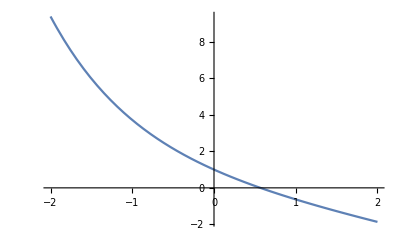

```mathematica
x = 0;
x1 = 1;
e = 0.00005;
Nmax = 15;
f[x_]:=  Exp[-x]-x;
If[f[x]*f[x1]>0,
Print["These vales do not satisfy the IVP so change the initial values"],
For[i=1,i≤Nmax,i++,a=N[(x *f[x1]- x1*f[x])/(f[x1]-f[x])];
If[f[a]f[x1]<0,x=a,x1=a];
If[Abs[x1-x]<e,Return[a]];
Print[i. "th iteration value is :",N[a]];
Print["Estimated error in ",i,"th iteration is: ",N[x1-x]]]]
Plot[f[x],{x,-2,2}]
```

5. Perform 15-iteration of Regula-Falsi method to Obtain the smallest positive root of f(x) = Sin[x]  in interval [0,1] and approx value x = 3, x1 = 4.

1.th iteration value is :3.15716

Estimated error in 1th iteration is: 0.157163

2.th iteration value is :3.14155

Estimated error in 2th iteration is: 0.0156165

Return[3.14159]

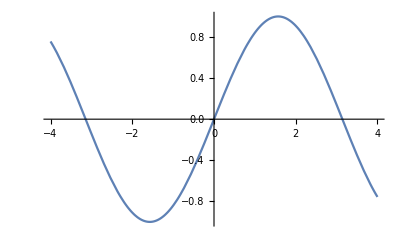

```mathematica
x = 3;
x1 = 4;
e = 0.00005;
Nmax = 15;
f[x_]:=  Sin[x];
If[f[x]*f[x1]>0,
Print["These vales do not satisfy the IVP so change the initial values"],
For[i=1,i≤Nmax,i++,a=N[(x *f[x1]- x1*f[x])/(f[x1]-f[x])];
If[f[a]f[x1]<0,x=a,x1=a];
If[Abs[x1-x]<e,Return[a]];
Print[i. "th iteration value is :",N[a]];
Print["Estimated error in ",i,"th iteration is: ",N[x1-x]]]]
Plot[f[x],{x,-4,4}]
```

1.th iteration value is :0.333333

Estimated error in 1th iteration is: 0.666667

2.th iteration value is :0.427562

Estimated error in 2th iteration is: 0.572438

3.th iteration value is :0.462648

Estimated error in 3th iteration is: 0.537352

4.th iteration value is :0.47665

Estimated error in 4th iteration is: 0.52335

5.th iteration value is :0.482369

Estimated error in 5th iteration is: 0.517631

6.th iteration value is :0.484725

Estimated error in 6th iteration is: 0.515275

7.th iteration value is :0.4857

Estimated error in 7th iteration is: 0.5143

8.th iteration value is :0.486103

Estimated error in 8th iteration is: 0.513897

9.th iteration value is :0.486271

Estimated error in 9th iteration is: 0.513729

10.th iteration value is :0.48634

Estimated error in 10th iteration is: 0.51366

11.th iteration value is :0.486369

Estimated error in 11th iteration is: 0.513631

12.th iteration value is :0.486381

Estimated error in 12th iteration is: 0.513619

13.th iteration value is :0.486386

Estimated error in 13th iteration is: 0.513614

14.th iteration value is :0.486388

Estimated error in 14th iteration is: 0.513612

15.th iteration value is :0.486388

Estimated error in 15th iteration is: 0.513612

16.th iteration value is :0.486389

Estimated error in 16th iteration is: 0.513611

17.th iteration value is :0.486389

Estimated error in 17th iteration is: 0.513611

18.th iteration value is :0.486389

Estimated error in 18th iteration is: 0.513611

19.th iteration value is :0.486389

Estimated error in 19th iteration is: 0.513611

20.th iteration value is :0.486389

Estimated error in 20th iteration is: 0.513611

21.th iteration value is :0.486389

Estimated error in 21th iteration is: 0.513611

22.th iteration value is :0.486389

Estimated error in 22th iteration is: 0.513611

23.th iteration value is :0.486389

Estimated error in 23th iteration is: 0.513611

24.th iteration value is :0.486389

Estimated error in 24th iteration is: 0.513611

25.th iteration value is :0.486389

Estimated error in 25th iteration is: 0.513611

26.th iteration value is :0.486389

Estimated error in 26th iteration is: 0.513611

27.th iteration value is :0.486389

Estimated error in 27th iteration is: 0.513611

28.th iteration value is :0.486389

Estimated error in 28th iteration is: 0.513611

29.th iteration value is :0.486389

Estimated error in 29th iteration is: 0.513611

30.th iteration value is :0.486389

Estimated error in 30th iteration is: 0.513611

31.th iteration value is :0.486389

Estimated error in 31th iteration is: 0.513611

32.th iteration value is :0.486389

Estimated error in 32th iteration is: 0.513611

33.th iteration value is :0.486389

Estimated error in 33th iteration is: 0.513611

34.th iteration value is :0.486389

Estimated error in 34th iteration is: 0.513611

35.th iteration value is :0.486389

Estimated error in 35th iteration is: 0.513611

36.th iteration value is :0.486389

Estimated error in 36th iteration is: 0.513611

37.th iteration value is :0.486389

Estimated error in 37th iteration is: 0.513611

38.th iteration value is :0.486389

Estimated error in 38th iteration is: 0.513611

39.th iteration value is :0.486389

Estimated error in 39th iteration is: 0.513611

40.th iteration value is :0.486389

Estimated error in 40th iteration is: 0.513611

41.th iteration value is :0.486389

Estimated error in 41th iteration is: 0.513611

Return[0.486389]

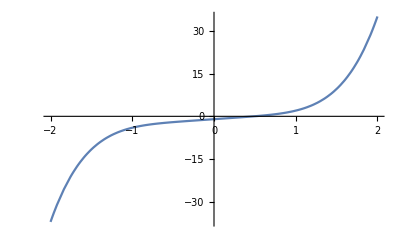

```mathematica
x = 0;
x1 = 1;
e = 0.00005;
Nmax = 43;
f[x_]:=  x^5+2x-1;
If[f[x]*f[x1]>0,
Print["These vales do not satisfy the IVP so change the initial values"],
For[i=1,i≤Nmax,i++,a=N[(x *f[x1]- x1*f[x])/(f[x1]-f[x])];
If[f[a]f[x1]<0,x=a,x1=a];
If[Abs[x1-x]<e,Return[a]];
Print[i. "th iteration value is :",N[a]];
Print["Estimated error in ",i,"th iteration is: ",N[x1-x]]]]
Plot[f[x],{x,-2,2}]
```